# Registration of identified sources in image and alignment to Yale Catalog

## Importing the source positions and the visible bright stars from python generated CSV

```mathematica
sources=Import[NotebookDirectory[]<>"sources.csv"];
(*Rescale source intensities to magnitude scale with arbitrary offset*)
sources={#⟦1⟧,#⟦2⟧,-2.5Log10[#⟦3⟧/Max[sources⟦;;,3⟧]]}&/@sources;
yale=Import[NotebookDirectory[]<>"yale.csv"];
```

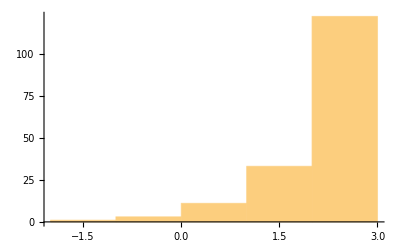

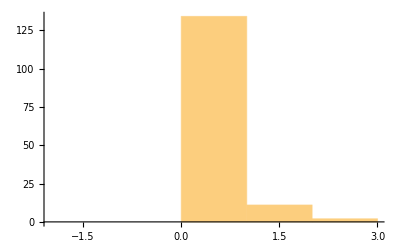

```mathematica
Histogram[yale⟦;;,3⟧,{-2,3,1}]
Histogram[sources⟦;;,3⟧,{-2,3,1}]
```

```mathematica
Min[yale⟦;;,2⟧]
```

-88.9564

## Projection used for Fisheye

```mathematica
Cases[Reduce[r==f ((1-Z)Sin[θ])/(Cos[θ]-Z),θ]/.C[1]->0,θ==_,Infinity]⟦-2;;⟧
%/.{f->1.55,Z->0.6,r->1}
```

{θ==2 ArcTan[(-f+f Z-√(-(-1+Z) (f^2+r^2-f^2 Z+r^2 Z)))/(r (1+Z))],θ==2 ArcTan[(-f+f Z+√(-(-1+Z) (f^2+r^2-f^2 Z+r^2 Z)))/(r (1+Z))]}

{θ==-1.59068,θ==0.480684}

```mathematica
2 ArcTan[f(-1+Z+√((1-Z)^2+(r/f)^2(1-Z^2)))/(r (1+Z))]
```

```mathematica
Factor[f(-1+Z+√((1-Z)^2+(r/f)^2(1-Z^2)))/(r (1+Z))]
```

(f (-1+Z+√(((-1+Z) (-f^2-r^2+f^2 Z-r^2 Z))/f^2)))/(r (1+Z))

```mathematica
f ((1-Z)Sin[θ])/(Cos[θ]-Z)/.Z->0
```

f Tan[θ]

## Transformation from horizontal frame to sensor frame

```mathematica
transform=p == {xc,yc}+Simplify[TrigExpand[{r Cos[ϕ], r Sin[ϕ]}/.{ϕ->A+ϕN,r->f Piecewise[{{Sin[k θ]/k, k<0}, {θ, k==0}, {((1-Z)Sin[θ])/(Cos[θ]-Z), True}}]}]/.({Sin[A]->-Sin[H]Cos[δ]/Cos[a],Cos[A]->(Sin[δ]-Sin[φ]Sin[a])/(Cos[φ]Cos[a])}/.a->π/2-θ)/.θ->ArcCos[Sin[δ]Sin[φ]+Cos[δ]Cos[φ]Cos[H]]]
```

p=={xc+(f (Piecewise[{{Sin[k ArcCos[Cos[H] Cos[δ] Cos[φ]+Sin[δ] Sin[φ]]]/k, k<0}, {ArcCos[Cos[H] Cos[δ] Cos[φ]+Sin[δ] Sin[φ]], k==0}, {((1-Z) √(1-(Cos[H] Cos[δ] Cos[φ]+Sin[δ] Sin[φ])^2))/(-Z+Cos[H] Cos[δ] Cos[φ]+Sin[δ] Sin[φ]), True}}]) (Cos[φ] Cos[ϕN] Sin[δ]+Cos[δ] (-Cos[H] Cos[ϕN] Sin[φ]+Sin[H] Sin[ϕN])))/(√(1-(Cos[H] Cos[δ] Cos[φ]+Sin[δ] Sin[φ])^2)),yc+(f (Piecewise[{{Sin[k ArcCos[Cos[H] Cos[δ] Cos[φ]+Sin[δ] Sin[φ]]]/k, k<0}, {ArcCos[Cos[H] Cos[δ] Cos[φ]+Sin[δ] Sin[φ]], k==0}, {((1-Z) √(1-(Cos[H] Cos[δ] Cos[φ]+Sin[δ] Sin[φ])^2))/(-Z+Cos[H] Cos[δ] Cos[φ]+Sin[δ] Sin[φ]), True}}]) (Cos[φ] Sin[δ] Sin[ϕN]-Cos[δ] (Cos[ϕN] Sin[H]+Cos[H] Sin[φ] Sin[ϕN])))/(√(1-(Cos[H] Cos[δ] Cos[φ]+Sin[δ] Sin[φ])^2))}

```mathematica
Simplify[(transform/.{φ->46.973141°,f->1.55,k->0,Z->0})//N]
```

p=={xc+(1.55 ArcCos[0.682341 Cos[H] Cos[δ]+0.731034 Sin[δ]] (-0.731034 Cos[H] Cos[δ] Cos[ϕN]+0.682341 Cos[ϕN] Sin[δ]+Cos[δ] Sin[H] Sin[ϕN]))/(√(1.-0.465589 (1. Cos[H] Cos[δ]+1.07136 Sin[δ])^2)),yc-(1.1331 ArcCos[0.682341 Cos[H] Cos[δ]+0.731034 Sin[δ]] (-0.933392 Sin[δ] Sin[ϕN]+Cos[δ] (1.36793 Cos[ϕN] Sin[H]+1. Cos[H] Sin[ϕN])))/(√(1.-0.465589 (1. Cos[H] Cos[δ]+1.07136 Sin[δ])^2))}

```mathematica
StringReplace[ToString[PiecewiseExpand[transform⟦2,#⟧,k<0]/.{δ->delta,ϕN->phiN,φ->lat,Cos[H] Cos[δ] Cos[φ]->cosHdj,Sin[φ]Sin[δ]->sindj}//FortranForm],{"ArcCos"->"acos","Sqrt"->"sqrt","Cos"->"cos","Sin"->"sin"}]&/@Range[1,2]
```

{xc + (f*(cos(lat)*cos(phiN)*sin(delta) + cos(delta)*(-(cos(H)*cos(phiN)*sin(lat)) + sin(H)*sin(phiN)))*sin(k*acos(cosHdj + sindj)))/(k*sqrt(1 - (cosHdj + sindj)**2)),yc + (f*(cos(lat)*sin(delta)*sin(phiN) - cos(delta)*(cos(phiN)*sin(H) + cos(H)*sin(lat)*sin(phiN)))*sin(k*acos(cosHdj + sindj)))/(k*sqrt(1 - (cosHdj + sindj)**2))}

```mathematica
StringReplace[ToString[PiecewiseExpand[transform⟦2,#⟧,k==0]/.{δ->delta,ϕN->phiN,φ->lat,Cos[H] Cos[δ] Cos[φ]->cosHdj,Sin[φ]Sin[δ]->sindj}//FortranForm],{"ArcCos"->"acos","Sqrt"->"sqrt","Cos"->"cos","Sin"->"sin"}]&/@Range[1,2]
```

{xc + (f*acos(cosHdj + sindj)*(cos(lat)*cos(phiN)*sin(delta) + cos(delta)*(-(cos(H)*cos(phiN)*sin(lat)) + sin(H)*sin(phiN))))/sqrt(1 - (cosHdj + sindj)**2),yc + (f*acos(cosHdj + sindj)*(cos(lat)*sin(delta)*sin(phiN) - cos(delta)*(cos(phiN)*sin(H) + cos(H)*sin(lat)*sin(phiN))))/sqrt(1 - (cosHdj + sindj)**2)}

```mathematica
StringReplace[ToString[PiecewiseExpand[transform⟦2,#⟧,k>0]/.{δ->delta,ϕN->phiN,φ->lat,Cos[H] Cos[δ] Cos[φ]->cosHdj,Sin[φ]Sin[δ]->sindj}//FortranForm],{"ArcCos"->"acos","Sqrt"->"sqrt","Cos"->"cos","Sin"->"sin"}]&/@Range[1,2]
```

{xc + (f*(1 - Z)*(cos(lat)*cos(phiN)*sin(delta) + cos(delta)*(-(cos(H)*cos(phiN)*sin(lat)) + sin(H)*sin(phiN))))/(cosHdj + sindj - Z),yc + (f*(1 - Z)*(cos(lat)*sin(delta)*sin(phiN) - cos(delta)*(cos(phiN)*sin(H) + cos(H)*sin(lat)*sin(phiN))))/(cosHdj + sindj - Z)}

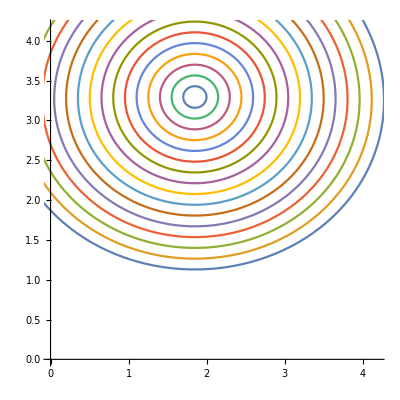

```mathematica
ParametricPlot[Evaluate[Table[transform⟦2⟧/.{φ->46.973141°,f->1.55,δ->d,k->0,xc->770/1000*2.4,yc->887/1000*2.4,Z->-2.2,ϕN->π/2},{d,10°,85°,5°}]],{H,0,2π},PlotRange->{{0,1744/1000*2.4},{0,1740/1000*2.4}},AspectRatio->1]
```

```mathematica
Expand[FullSimplify[PiecewiseExpand[transform⟦2⟧,k<0]/.{k->-1,ϕN->π/2}],H]/.{-f Cos[δ]Sin[φ]->aE,f Cos[δ]->bE,xc->dx,yc->dy-f Cos[φ]Sin[δ]}
```

{dx+bE Sin[H],dy+aE Cos[H]}

## Fit Ellipse through Morphological Components

## Select Morphological components which seem to be strong startrails (by elongation and # ov pixels)

```mathematica
startrails=Import[NotebookDirectory[]<>"..\\tests\\startrails20191229.png"];
components=MorphologicalComponents[startrails,0.5];
components=Last[SelectComponents[{startrails,components},#Count>400&&#Elongation>0.8&]];
indx=Rest[Tally[Flatten[components]]]
```

{{80,793},{100,553},{339,1198},{428,3316},{646,1232},{449,600},{514,1548},{537,1067},{636,4888},{573,2202},{802,491},{916,2340},{970,2711},{989,2799},{1574,2764},{1209,1437},{1283,1499},{1429,3735},{1512,2649},{1518,461},{1557,1272},{1637,1231},{1656,498},{1741,5307}}

```mathematica
{{Min[#⟦;;,1⟧],Max[#⟦;;,1⟧]},{Min[#⟦;;,2⟧],Max[#⟦;;,2⟧]}}&@Table[Round[transform⟦2⟧*1000/2.4/.{φ->46.973141 °,f->1.55,δ->85.°,H->x 1.,k->-0,Z->-2.2,ϕN->π/2}/.Thread[Rule[{xc,yc},Most[ImageMeasurements[startrails,"Dimensions"]]/2*2.4/1000]]],{x,0,3π/2,π/2}]
```

{{842,966},{1333,1445}}

```mathematica
startrails=Import[NotebookDirectory[]<>"..\\tests\\startrails20200102.png"];
Show[MorphologicalComponents[startrails,0.5]//Colorize,Graphics[{FaceForm[None],EdgeForm[White],Rectangle@@({{Min[#⟦;;,1⟧],Min[#⟦;;,2⟧]},{Max[#⟦;;,1⟧],Max[#⟦;;,2⟧]}}&@Table[Round[transform⟦2⟧*1000/2.4/.{φ->46.973141 °,f->1.55,δ->87.°,H->x 1.,k->-0,Z->-2.2,ϕN->π/2+0.8°}/.Thread[Rule[{xc,yc},Most[ImageMeasurements[startrails,"Dimensions"]]/2*2.4/1000]]],{x,0,3π/2,π/2}]),EdgeForm[Green],Polygon[Table[Round[transform⟦2⟧*1000/2.4/.{φ->46.973141 °,f->1.55,δ->87.°,H->x 1.,k->-0,Z->-2.2,ϕN->π/2+0.8°}/.Thread[Rule[{xc,yc},Most[ImageMeasurements[startrails,"Dimensions"]]/2*2.4/1000]]],{x,0,2π,π/50}]]}]]
```

-Graphics-

## Fit Ellipse through startrail

See StackExchange answer on how to fit an tilted off center ellipse through a set of points.